Routines for YODA plotting

from: https://yoda.hepforge.org/trac/wiki/DataFormat

```mathematica
<<(NotebookDirectory[]<>"../../atom_mathematica.m")
```

1 Imported ..Histo1D..  /ATLAS_1407_3935/Mmm/0

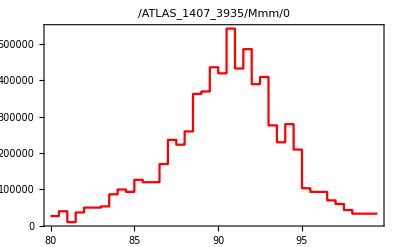

```mathematica
Zmm=(GetYodaRaw[NotebookDirectory[]<>"Zmm.yoda"]);
F1=HistogramPlot[Zmm[[1]],PlotStyle->{Red}]
```

1 Imported ..Scatter2D..  /REF/ATLAS_1008_2461/d01-x01-y01

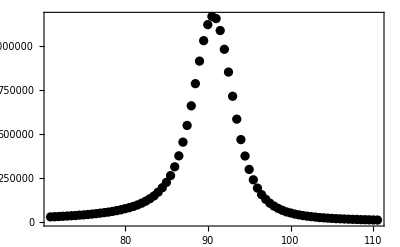

```mathematica
ATLAS=(GetYodaRaw[NotebookDirectory[]<>"ATLAS_Zmm.yoda"]);
F2=ScatterPlot[ATLAS[[1]],PlotStyle->{Black}]
```

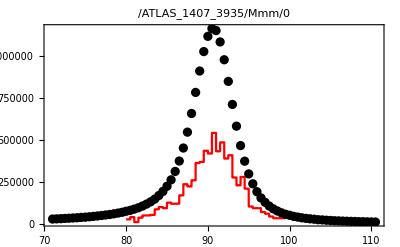

```mathematica
Show[{F1,F2}]
```